```mathematica
ch=0(*10^-12*);
µ=0;
kp=0;
Φ=(rp*ch)/r^2;
g=((r^2-rp^2)/L^2);
V[r_]=g/4(-g/(4 r^2)+D[g,r]/(2r)+kp^2/r^2+µ^2)-Φ^2/4;
P2a[r_]=-ⅈ Φ/2;
```

```mathematica
fch[r_]=Re[∫1/g ⅆr];
```

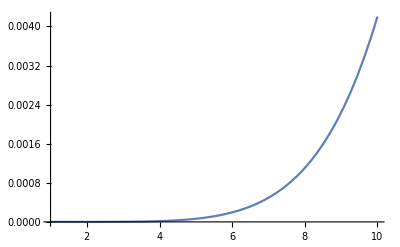

```mathematica
Plot[Re[V[r]],{r,rp,10rp}]
```

```mathematica
P=Table[0,{i,1,(te-ts)/h+2,1}];
P2=Table[0,{i,1,(te-ts)/h+2,1}];
Do[P[[i]]=V[tort[[i]]],{i,1,(te-ts)/h+1,1}];
Do[P2[[i]]=P2a[tort[[i]]],{i,1,(te-ts)/h+1,1}];
```

```mathematica
(*Profile[x_]=N[Exp[-x^2],Mp];
s=Table[Profile[i],{i,0,(te-ts)/h+5,1}];*)
s=Table[0,{i,0,(te-ts)/h+5,1}];
s[[1]]=1;(*Profile[Abs[(ts+te)]/2];*)
Fd=Table[0,{i,0,(te-ts)/h+5,1}];
LFd=Table[0,{i,0,(te-ts)/h+5,1}];
```

```mathematica
kpp=0;
seg=Length[s]/10;
len=Length[P];
```

```mathematica
(*Integration*)
kpp=0; 
seg=400;
Timing[For[i=0,i<k2+k1-3,i++,
var=s[[1]];
s[[1]]=1;
If[IntegerPart[i/seg]==i/seg,Print[i],kpp=kpp+1];
For[j=2,j≤i+2,j++,
tmp=s[[j]];
If[j==i+2,s[[j]]==0];
s[[j]]=SetPrecision[(s[[j-1]]+s[[j]]-var(1-2h*P2[[j+k2+k1-i-2]])
-(2)h^2*(P[[j+k2+k1-i-3]]*s[[j-1]]+P[[j+k2+k1-i-1]]*s[[j]]))*(2h*P2[[j+k1+k2-i-2]]+1)^-1,Mp];
var=tmp;
If[j==i+2;LFd[[j-1]]=Log[s[[j]]^2]/2;Fd[[j-1]]=s[[j]],kpp=kpp+1];
]];]
```

0

400

800

1200

1600

2000

2400

2800

3200

3600

4000

4400

4800

5200

5600

6000

6400

6800

7200

7600

8000

8400

8800

9200

9600

{1776.88,Null}

```mathematica
v1=Length[LFd]
```

10005

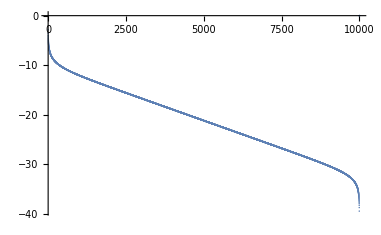

```mathematica
yz=ListPlot[Re[LFd[[1;;v1]]]]
```

```mathematica
(*LinearRegession*)
lee=Floor[3v1/5];
le=Floor[4v1/5];
la=le-lee;
LogFd=Table[Log[Re[s[[i]]]^2]/2,{i,1,le}];
(*Field=Table[Log[Profile1[[i,2]]^2]/2,{i,1,Length[Profile1]}];*)
Field=Table[LogFd[[i]],{i,1,le}];
Fieldt=Table[2h*i,{i,1,le}];
xsum=∑_(i=lee)^le (Fieldt[[i]]) ;(*time*)
ysum=∑_(i=lee)^le (Field[[i]]);(*Log Field*)
xsumsq=∑_(i=lee)^le (Fieldt[[i]])^2;
ysumsq=∑_(i=lee)^le (Field[[i]])^2;
xy=∑_(i=lee)^le (Fieldt[[i]]*Field[[i]] );
A=((le-lee+1)*xy-xsum*ysum)/((le-lee+1)*xsumsq - xsum^2);B=(ysum*xsumsq-xsum*xy)/((le-lee+1)*xsumsq - xsum^2);
(*Errors*)
dey = ∑_(i=lee)^le (Field[[i]]-A*Fieldt[[i]]-B )^2;

sig= √(dey/((le-lee+1)-2));sigA=sig√((le-lee+1)/((le-lee+1)*xsumsq-xsum^2));DeWI=sigA;
sigB=sig√(xsumsq/((le-lee+1)*xsumsq-xsum^2));
R=((le-lee+1)xy-xsum*ysum)/(√(((le-lee+1)xsumsq-xsum^2)((le-lee+1)ysumsq-ysum^2)));
A
```

-0.00011212543843257934180012946514465232745660136892535651896011662694310570487075550284632111714197151848122177397258139829527670566040334745453765475795583030829561712220406130613925276520734985446568413995595514219716979999406097918130836299082766637